```mathematica
leanAssoc=CloudGet["https://wolfr.am/PL39QRbE"];
```

```mathematica
leanGraph=CloudGet["https://wolfr.am/PL3LfaQ4"];
```

Idea is to use the existing Graph/Association (2020) for now, where a direct/new import from the current Mathlib might be helpful (bridge extension, as a function) later on. Stephen referred me to Mano about how to actually get the data. A comparison of the project in 2020 vs now, 2023, might be interesting.

```mathematica
leanDomains = Union[Values[leanAssoc]];
leanDomains
```

{algebra,algebraic_geometry,analysis,category_theory,combinatorics,computability,control,data,dynamics,geometry,init,logic,meta,number_theory,order,set_theory,system,tactic,topology}

```mathematica
leanInfrastructure = {"init", "system", "tactic", "data", "meta", "control", "computability"};
leanInfrastructure
```

{init,system,tactic,data,meta,control,computability}

```mathematica
leanColors = Merge[{AssociationThread[Complement[leanDomains, leanInfrastructure] -> Take[ColorData[54, "ColorList"], Length[Complement[leanDomains, leanInfrastructure]]]], AssociationThread[leanInfrastructure -> LightGray]}, Identity];
leanColors
```

<|algebra→{RGBColor[0.782803, 0.164904, 0.400458]},algebraic_geometry→{RGBColor[0.909499, 0.613916, 0.204196]},analysis→{RGBColor[0.806577, 0.385397, 0.762768]},category_theory→{RGBColor[0.698817, 0.873304, 0.295247]},combinatorics→{RGBColor[0.378897, 0.873304, 0.787549]},dynamics→{RGBColor[1, 0.529198, 0.324819]},geometry→{RGBColor[1, 0.998367, 0.434775]},logic→{RGBColor[0.873304, 0.150484, 0.255131]},number_theory→{RGBColor[0.723598, 0.791043, 0.963806]},order→{RGBColor[0.85037, 0.558389, 0]},set_theory→{RGBColor[1, 0.998856, 0.00207523]},topology→{RGBColor[0.273106, 0.542992, 0.495583]},init→{GrayLevel[0.85]},system→{GrayLevel[0.85]},tactic→{GrayLevel[0.85]},data→{GrayLevel[0.85]},meta→{GrayLevel[0.85]},control→{GrayLevel[0.85]},computability→{GrayLevel[0.85]}|>

```mathematica
leanDomainWeights = Tally[Values[leanAssoc]];
leanDomainWeights (* theorem keys tallied by category (value) *)
```

{{algebra,8355},{analysis,4021},{geometry,559},{tactic,396},{init,1293},{data,11165},{computability,589},{combinatorics,108},{order,1903},{topology,3220},{logic,483},{category_theory,1834},{number_theory,266},{set_theory,1096},{dynamics,161},{algebraic_geometry,70},{meta,9},{control,161},{system,1}}

```mathematica
leanEdgeWeights = Tally[{leanAssoc[#[[1]]], leanAssoc[#[[2]]]} & /@ EdgeList[leanGraph]];
leanEdgeWeights
```

{{{data,init},27512},{{data,data},20902},{{topology,topology},5055},{{algebra,algebra},16771},{{computability,computability},1870},{{set_theory,set_theory},2507},{{data,algebra},6184},{{topology,order},1493},{{init,init},3493},{{tactic,init},1099},{{analysis,init},8734},{{algebra,init},13441},{{order,init},2843},{{number_theory,init},1157},{{analysis,analysis},7831},{{algebra,data},4175},{{number_theory,algebra},697},{{geometry,geometry},954},{{analysis,algebra},4845},{{geometry,data},671},{{number_theory,number_theory},446},{{topology,init},5122},{{computability,init},1706},{{category_theory,init},1812},{{set_theory,init},2418},{{geometry,init},1202},{{combinatorics,init},353},{{dynamics,init},268},{{logic,init},487},{{control,init},447},{{algebraic_geometry,init},74},{{algebraic_geometry,algebra},26},{{order,data},661},{{number_theory,tactic},544},{{computability,data},905},{{order,order},3070},{{analysis,tactic},2073},{{analysis,data},2720},{{analysis,topology},1643},{{tactic,algebra},421},{{set_theory,algebra},254},{{tactic,logic},33},{{tactic,data},151},{{order,algebra},69},{{topology,data},2397},{{data,analysis},34},{{analysis,order},853},{{set_theory,data},303},{{data,tactic},1671},{{category_theory,category_theory},1462},{{number_theory,data},417},{{topology,algebra},809},{{logic,logic},295},{{algebra,order},656},{{dynamics,algebra},140},{{data,order},441},{{algebra,set_theory},121},{{geometry,topology},380},{{data,logic},1617},{{algebraic_geometry,algebraic_geometry},46},{{dynamics,dynamics},199},{{topology,logic},335},{{algebra,logic},658},{{set_theory,order},49},{{control,control},128},{{computability,logic},190},{{algebraic_geometry,topology},11},{{algebra,tactic},655},{{combinatorics,data},138},{{geometry,algebra},424},{{geometry,tactic},167},{{set_theory,logic},140},{{tactic,tactic},263},{{combinatorics,combinatorics},114},{{geometry,logic},26},{{analysis,combinatorics},32},{{order,logic},221},{{data,set_theory},33},{{geometry,analysis},214},{{category_theory,algebra},53},{{algebra,control},6},{{topology,control},8},{{dynamics,topology},44},{{combinatorics,algebra},42},{{topology,analysis},23},{{analysis,logic},228},{{topology,tactic},198},{{category_theory,data},39},{{topology,category_theory},34},{{algebraic_geometry,data},19},{{category_theory,logic},18},{{dynamics,analysis},6},{{data,control},35},{{algebra,category_theory},46},{{combinatorics,logic},9},{{geometry,order},23},{{dynamics,logic},28},{{dynamics,order},28},{{analysis,set_theory},2},{{set_theory,tactic},45},{{data,topology},17},{{computability,algebra},42},{{control,data},23},{{dynamics,data},22},{{algebraic_geometry,logic},3},{{meta,init},4},{{system,data},3},{{system,init},2},{{number_theory,order},5},{{combinatorics,order},2},{{algebraic_geometry,category_theory},11},{{algebraic_geometry,order},13},{{number_theory,logic},24},{{computability,control},3},{{topology,dynamics},5},{{system,logic},1},{{category_theory,tactic},7},{{order,tactic},21},{{dynamics,tactic},2},{{logic,tactic},4},{{combinatorics,tactic},5},{{logic,data},2},{{control,logic},7},{{algebraic_geometry,tactic},1},{{topology,set_theory},4},{{data,number_theory},1},{{order,control},1}}

```mathematica
leanEdgesOutSimple = Append[Merge[AssociationThread[{#[[1, 1, 1]]}-> Total[#[[2]]]] & /@ (Transpose /@ GatherBy[Select[leanEdgeWeights, #[[1, 1]] ≠ #[[1, 2]] &], #[[1, 1]] &]), Identity], "init" -> {3493}];
leanEdgesOutSimple
```

<|data→{37545},topology→{10428},tactic→{1704},analysis→{21130},algebra→{19758},order→{3816},number_theory→{2844},geometry→{3107},computability→{2846},category_theory→{1929},set_theory→{3209},combinatorics→{549},dynamics→{538},logic→{493},control→{477},algebraic_geometry→{158},meta→{4},system→{6},init→{3493}|>

```mathematica
leanNormalizedEdgeWeights = DirectedEdge[#[[1, 1]], #[[1, 2]]] -> #[[2]]/ Flatten[leanEdgesOutSimple[#[[1,1]]]] & /@ leanEdgeWeights;
```

```mathematica
diskedLine[{line_,radii_}]:={RegionIntersection[Line[line],Circle[line[[1]],radii[[1]]]][[1,1]],
RegionIntersection[Line[line],Circle[line[[2]],radii[[2]]]][[1,1]]};
```

```mathematica
weightedArrow[line_,weight_]:= Module[{len,start,end,angle, thick, rec, mid},
start=line[[1]]; end=line[[2]]; mid=Mean[line];
len=EuclideanDistance[start,end];
angle=Arg[(start-end).{1,I}];
thick=weight/len;
rec= #+mid&/@(RotationMatrix[angle].#&/@{{-len/2,- thick/2},{len/2,- thick/2},{len/2, thick/2},{-len/2, thick/2}});
Polygon[rec]];
```

```mathematica
VertexDelete[SimpleGraph[Graph[leanDomains, First /@ leanNormalizedEdgeWeights, EdgeStyle->Thread[First/@leanNormalizedEdgeWeights -> ({AbsoluteThickness[20Last[#][[1]]],Arrowheads[Last[#][[1]]/4], GrayLevel[0.5, 0.5]}&/@leanNormalizedEdgeWeights)], VertexSize->Thread[First/@leanDomainWeights -> (Sqrt[#]/90&/@(Last/@leanDomainWeights))], VertexStyle -> (# -> {Lighter /@ leanColors[#]} & /@  leanDomains),  VertexLabels->{"algebra" -> "algebra","algebraic_geometry" -> "algebraic geometry","analysis" -> "analysis","category_theory" -> "category theory","combinatorics" -> "combinatorics","computability" -> "computability","control" -> "control","data" -> "data","dynamics" -> "dynamics","geometry" -> "geometry","init" -> "init","logic" -> "logic","meta" -> "meta","number_theory" -> "number theory","order" -> "order theory","set_theory" -> "set theory","system" -> "system","tactic" -> "tactic","topology" -> "topology"}, GraphLayout -> "SpringElectricalEmbedding", PerformanceGoal->"Quality", AspectRatio->1/4]], {"init", "system", "tactic", "data", "meta", "control", "computability"}, AspectRatio-> 1]
```

-Graphics-

```mathematica
Column[Rest[VertexOutComponent[leanGraph,"euclidean_geometry.dist_square_eq_dist_square_add_dist_square_iff_angle_eq_pi_div_two",1]],Frame->All,FrameStyle->GrayLevel[.7], With[{leanA=leanAssoc[#] & /@ Rest[VertexOutComponent[leanGraph,"euclidean_geometry.dist_square_eq_dist_square_add_dist_square_iff_angle_eq_pi_div_two",1]]},Background -> (Lighter[#,0.5]& /@ Flatten[leanColors[#] & /@leanA])]]
```

inner_product_geometry.norm_sub_square_eq_norm_square_add_norm_square_iff_angle_eq_pi_div_two
norm_neg
eq.symm
iff.refl
vsub_sub_vsub_cancel_right
dist_eq_norm_vsub
neg_vsub_eq_vsub_rev

```mathematica
Subgraph[leanGraph, VertexOutComponent[leanGraph,"euclidean_geometry.dist_square_eq_dist_square_add_dist_square_iff_angle_eq_pi_div_two"],1]
```

```mathematica
leanDomains = Union[Values[leanAssoc]];
```

```mathematica
leanInfrastructure = {"init", "system", "tactic", "data", "meta", "control", "computability"};
```

```mathematica
leanColors = Merge[{AssociationThread[Complement[leanDomains, leanInfrastructure] -> Take[ColorData[54, "ColorList"], Length[Complement[leanDomains, leanInfrastructure]]]], AssociationThread[leanInfrastructure -> LightGray]}, Identity];
```

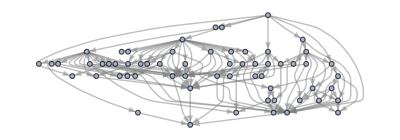

```mathematica
Legended[Subgraph[leanGraph,VertexOutComponent[leanGraph,"euclidean_geometry.dist_square_eq_dist_square_add_dist_square_iff_angle_eq_pi_div_two",3],GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/3, EdgeStyle-> GrayLevel[0.5, 0.5], VertexStyle -> (# -> {Lighter /@ leanColors[leanAssoc[#]]} & /@  VertexList[leanGraph]), VertexSize -> 0.75], SwatchLegend[Flatten[Lighter /@ leanColors[#] & /@ {"algebra","analysis","geometry","init","tactic","topology"}], {"algebra","analysis","geometry","init","tactic","topology"}]]
```

```mathematica
leanGraph = CloudGet["https://wolfr.am/PL3LfaQ4"];
```

```mathematica
metamathGraph =CloudGet["https://wolfr.am/PLbmdhRv"];
```

```mathematica
euc=ResourceData["Theorem Network from Euclid's Elements"];
```

Histogram::ldata: VertexOutDegree[metamathGraph] is not a valid dataset or list of datasets.

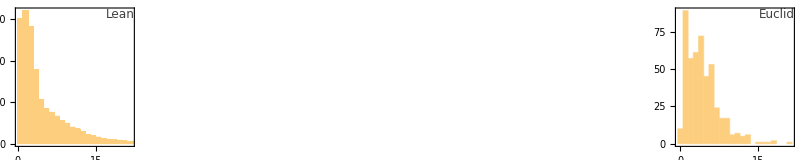

```mathematica
GraphicsRow[Histogram[Last[#],Frame->True,ImageSize->250,Epilog->Text[Style[First[#],Directive[FontSize->12,GrayLevel[0.25],FontFamily->"Source Sans Pro"]],Scaled[{1,1}],{1.5,1.4}]]&/@{{"Lean",VertexOutDegree[leanGraph]},{"Metamath",VertexOutDegree[metamathGraph]},{"Euclid",VertexOutDegree[euc]}}]
```

Alternative Theorem Tests

```mathematica
Column[Rest[VertexOutComponent[leanGraph,"euclidean_geometry.dist_square_eq_dist_square_add_dist_square_iff_angle_eq_pi_div_two",1]],Frame->All,FrameStyle->GrayLevel[.7], With[{leanA=leanAssoc[#] & /@ Rest[VertexOutComponent[leanGraph,"euclidean_geometry.dist_square_eq_dist_square_add_dist_square_iff_angle_eq_pi_div_two",1]]},Background -> (Lighter[#,0.5]& /@ Flatten[leanColors[#] & /@leanA])]]
```